# A very quick particle packing algorithm

T J Atherton

## Create some particles on a sphere

Number of particles

```mathematica
Np=20;
```

```mathematica
xrandom=Table[{2Random[]-1,2Random[]-1,2Random[]-1},{i,Np}];
```

```mathematica
x0=Map[#/Norm[#]&,xrandom];
```

```mathematica
r0=Table[1*^-2,{i,Np}];
```

## Visualize a configuration

```mathematica
visualizeConfig[x_,r_]:=Graphics3D[Join[Table[Sphere[x⟦i⟧,r⟦i⟧],{i,Length[x]}],{Gray,Sphere[{0,0,0}]}],Boxed->False]
```

```mathematica
visualizeConfig[x0,r0]
```

-Graphics3D-

## Diffusion on a sphere

```mathematica
sphericalDiffuse[x_,δ_]:=Block[{dx,xnew},
(* Move the particle along the tangent plane by a certain amount *)

(* Step 1: generate a move in 3D space *)
dx=RandomVariate[NormalDistribution[0,δ],3]; (* We need a normally-distributed point in 3D, not one randomly distributed in each axis *)

(* Step 2: Locally the surface normal of a sphere is parallel to x; so subtract the component of dx that is parallel to x and hence the surface normal. The move is now along the tangent plane *)
dx=dx- (dx.x) x/(x.x);

(* Step 3: Move *)
xnew=x+dx;

(* Step 4: Reproject onto sphere *)
xnew = xnew/Sqrt[xnew.xnew]
]
```

Test this

```mathematica
xa={1,0,0};rr=Reap[Do[Sow[xa=sphericalDiffuse[xa,0.02]],{i,1000}]];
```

And we have a nice random walk

```mathematica
Graphics3D[{Sphere[{0,0,0},0.99],Line[rr⟦2,1⟧]},Boxed-> False]
```

-Graphics3D-

## Diffusion sweeps including overlap prevention

```mathematica
diffusionSweep[x_,r_,δ_]:=Block[{xnew=x,xold,nrst,success=0}, (*should randomize order of indices*)
Do[
xold=xnew⟦i⟧;
xnew⟦i⟧=sphericalDiffuse[xnew⟦i⟧,δ];

(* Find the index of the nearest particle *)
nrst=Last[Nearest[MapIndexed[#-> #2⟦1⟧&,xnew],xnew⟦i⟧,2]];

(* If the move causes overlap, reject it *)
If[Norm[xnew⟦i⟧-xnew⟦nrst⟧]<r⟦i⟧+r⟦nrst⟧,xnew⟦i⟧=xold,success++];(*only works for uniform particle radii,needs a more advanced check otherwise*)

,{i,Length[x]}];

Return[{xnew,success}]
]
```

Test this

```mathematica
rb=Table[0.4,{i,Length[x0]}]; (* Set an intentionally large radius *)
xb=x0;
rr2=Reap[Do[Sow[xb=diffusionSweep[xb,rb,0.1]⟦1⟧],{i,100}]];
```

```mathematica
Graphics3D[Table[{Hue[i/Length[xb]],Line[Transpose[rr2⟦2,1⟧]⟦i⟧]},{i,Length[xb]}],Boxed-> False]
```

-Graphics3D-

## Inflation + Diffusion sweeps

```mathematica
rc=r0; 
xc=x0;
δc=0.03;

ap=Reap[Do[
{xc,ar}=diffusionSweep[xc,rc,δc]; (* Diffuse *)

Sow[ar/Length[xc]]; (* Sow the number of moves accepted *)

If[ar==0,Break[]];(* Stop once the acceptance ratio is zero *) (* Possibly look for a better convergence criterion *)

rc=Map[#+0.0005&,rc]; (* Inflate *) (* Possibly better inflation strategy [esp. b/c it's only good for identical radii] *)

,{i,2000}]];
```

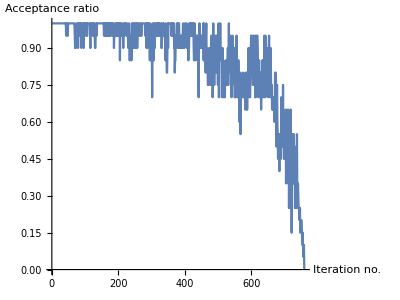

```mathematica
ListPlot[ap⟦2,1⟧,Joined-> True,AxesLabel->{"Iteration no.","Acceptance ratio"},AspectRatio->3/4]
```

Calculate approximate packing fraction (since we’re packing onto a unit sphere, its total surface area is 4π).

```mathematica
packingFraction=Total[Map[Pi #^2&,rc]]/(4 Pi)
```

0.758551

```mathematica
Show[visualizeConfig[xc,rc],Boxed->False] (*compare with possible "ideal" packings [platonic solids, etc]*)
```

-Graphics3D-

Some other ideas: plotting packing fraction vs. run time for various variations